```mathematica
FullSimplify[-D[A0 r^2+(B0 r^2 +C0)Log[r/R],r]]
```

-C0/r-(2 A0+B0) r-2 B0 r Log[r/R]

```mathematica
FullSimplify[-D[I0 r^2+I1 r^2 Log[r/R]+I2 Log[r/R]+I3,r]]
```

-I2/r-(2 I0+I1) r-2 I1 r Log[r/R]

```mathematica
FullSimplify[-D[A1 r+B1/r+B1p r θ+C1 r^3+D1 r Log[r/R],r]]
```

(B1-r^2 (A1+D1+3 C1 r^2+B1p θ))/r^2-D1 Log[r/R]

```mathematica
FullSimplify[-D[An r^n+Bn/r^n+Cn r^(n+2)+Dn/r^(n-2),r]]
```

r^(-1-n) (Bn n+Dn (-2+n) r^2-r^(2 n) (An n+Cn (2+n) r^2))

```mathematica
Integrate[θ Exp[-I k θ],{θ,0,2π}]
```

(-1+ⅇ^(-2 ⅈ k π) (1+2 ⅈ k π))/k^2

```mathematica
Integrate[θ ,{θ,0,2π}]
```

2 π^2

```mathematica
FullSimplify[(-1+ⅇ^(-2 ⅈ k π) (1+2 ⅈ k π))/k^2,Assumptions->k∈Integers]
```

(2 ⅈ π)/k

```mathematica
Manipulate[
Show[
Plot[π+Sum[I/n Exp[I n x],{n,-N1,-1}]+Sum[I/n Exp[I n x],{n,1,N1}],{x,0,2π}],
Plot[x,{x,0,2π},PlotStyle->Red]
]
,{N1,3,200,1}
]
```

```mathematica
Integrate[Sin[θ]Exp[-I k θ],{θ,0,2π}]
```

(-1+ⅇ^(-2 ⅈ k π))/(-1+k^2)

```mathematica
FullSimplify[(-1+ⅇ^(-2 ⅈ k π))/(-1+k^2),Assumptions->k∈ Integers]
```

0

```mathematica
Limit[(-1+ⅇ^(-2 ⅈ k π))/(-1+k^2),k->0]
```

0

```mathematica
Integrate[Sin[θ],{θ,0,2π}]
```

0

```mathematica
Integrate[Cos[θ]Exp[-I k θ],{θ,0,2π}]
```

(ⅈ (1-ⅇ^(-2 ⅈ k π)) k)/(1-k^2)

```mathematica
Integrate[Sin[θ]Exp[-I θ],{θ,0,2π}]
```

-ⅈ π

```mathematica
Integrate[Sin[θ]Exp[I θ],{θ,0,2π}]
```

ⅈ π

```mathematica
Integrate[Cos[θ]Exp[-I θ],{θ,0,2π}]
```

π

```mathematica
Integrate[Cos[θ]Exp[I θ],{θ,0,2π}]
```

π

```mathematica
Integrate[Cos[θ],{θ,0,2π}]
```

0

```mathematica
Integrate[θ Sin[θ]Exp[-I k θ],{θ,0,2π}]
```

(ⅇ^(-2 ⅈ k π) (2 ⅈ (-1+ⅇ^(2 ⅈ k π)) k-2 π+2 k^2 π))/((-1+k^2)^2)

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ k π) (2 ⅈ (-1+ⅇ^(2 ⅈ k π)) k-2 π+2 k^2 π))/((-1+k^2)^2),Assumptions->k∈ Integers]
```

(2 π)/(-1+k^2)

```mathematica
Integrate[θ Sin[θ],{θ,0,2π}]
```

-2 π

```mathematica
Integrate[θ Cos[θ]Exp[-I k θ],{θ,0,2π}]
```

(-1-k^2+ⅇ^(-2 ⅈ k π) (1+k^2+2 ⅈ k (-1+k^2) π))/((-1+k^2)^2)

```mathematica
FullSimplify[(-1-k^2+ⅇ^(-2 ⅈ k π) (1+k^2+2 ⅈ k (-1+k^2) π))/((-1+k^2)^2),Assumptions->k∈ Integers]
```

(2 ⅈ k π)/(-1+k^2)

```mathematica
Integrate[θ Cos[θ],{θ,0,2π}]
```

0

```mathematica
Integrate[θ Cos[θ]Exp[-I θ],{θ,0,2π}]
```

(ⅈ π)/2+π^2

```mathematica
Integrate[θ Cos[θ]Exp[I θ],{θ,0,2π}]
```

-(ⅈ π)/2+π^2

```mathematica
Integrate[θ Sin[θ]Exp[-I θ],{θ,0,2π}]
```

1/2 (-1-2 ⅈ π) π

```mathematica
Integrate[θ Sin[θ]Exp[I θ],{θ,0,2π}]
```

1/2 (-1+2 ⅈ π) π

```mathematica
Manipulate[NIntegrate[Sec[θ]/(1+Tan[θ]^n)^(1/n)Exp[-I k θ],{θ,0,2π}],{n,2,10},{k,1,10,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.155194+1.02952 ⅈ and 0.0811977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273773+0.00292141 ⅈ and 0.0339758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000556911+0.460004 ⅈ and 0.0370941 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

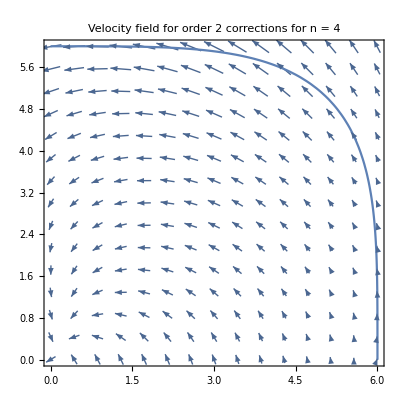

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=4; (* The velocity of the conveyor belt *)
R=6; (* The span of the conveyor belt *)
r=2; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=4; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.155194+1.02952 ⅈ and 0.0811977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273773+0.00292141 ⅈ and 0.0339758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000556911+0.460004 ⅈ and 0.0370941 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

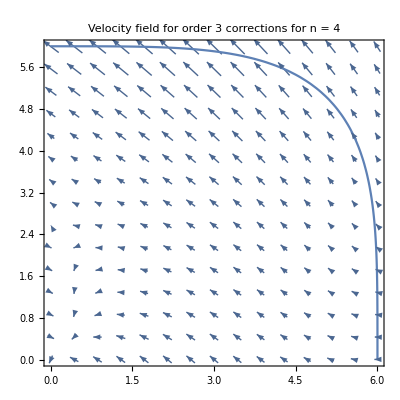

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=4; (* The velocity of the conveyor belt *)
R=6; (* The span of the conveyor belt *)
r=3; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=4; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.224658+0.937914 ⅈ and 0.0839217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0027378+0.00294045 ⅈ and 0.034719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000556785+0.609945 ⅈ and 0.0388983 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

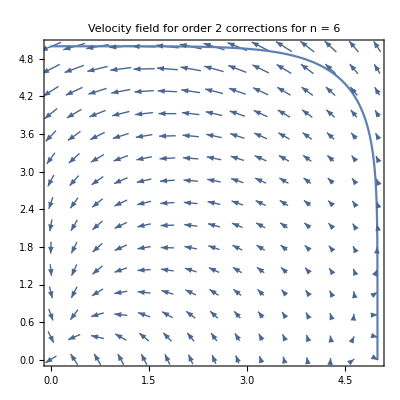

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=1; (* The velocity of the conveyor belt *)
R=5; (* The span of the conveyor belt *)
r=2; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=6; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.001R,0.999R},{y,0.001R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.257196+0.896236 ⅈ and 0.0851383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273781+0.00294264 ⅈ and 0.0324295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000556703+0.673952 ⅈ and 0.0399531 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

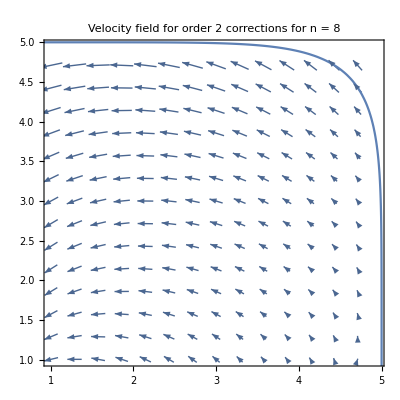

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=1; (* The velocity of the conveyor belt *)
R=5; (* The span of the conveyor belt *)
r=2; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=8; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.201R,0.999R},{y,0.201R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0.2R,0.99R},{0.2R,0.99R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.36778}. NIntegrate obtained -0.0601842+0.809943 ⅈ and 0.37229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.36778}. NIntegrate obtained 0.00589015+0.00578477 ⅈ and 0.0830485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.36778}. NIntegrate obtained 0.00484131+0.44993 ⅈ and 0.208985 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

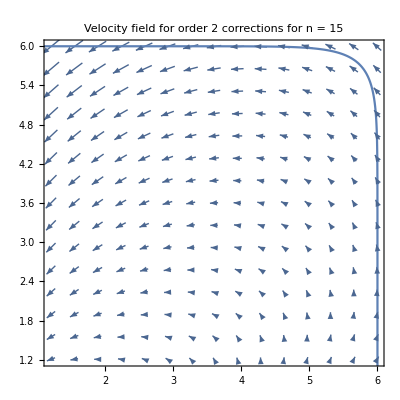

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=4; (* The velocity of the conveyor belt *)
R=6; (* The span of the conveyor belt *)
r=2; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=15; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.201R,0.999R},{y,0.201R,0.999R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0.2R,R},{0.2R,R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.300544+0.840973 ⅈ and 0.0943831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0000214661+0.00590353 ⅈ and 0.0638203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000536304+0.753279 ⅈ and 0.078301 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

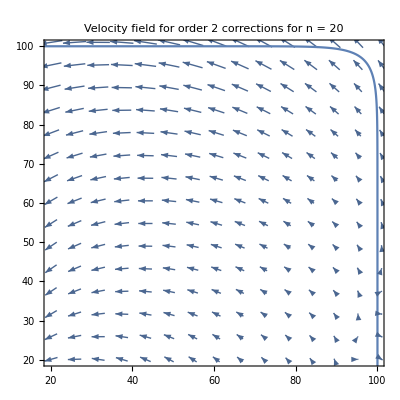

```mathematica
Block[
{U,R,r,M,n,A,B,C1,I1,E1,F,G,f1,f2,f3,f4,f5,f6,f7,f8,eq1,eq2,soln,ur,uθ},
U=1; (* The velocity of the conveyor belt *)
R=100; (* The span of the conveyor belt *)
r=2; (* The number of correction oscillations *)
M=10+r; (* The number of integration constants, M≥11 *)
n=20; (* Curvature exponent *)
f1[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f2[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
f3[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^2 Sin[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f4[k_]:=NIntegrate[Exp[-I k θ]Sec[θ]/(1+Tan[θ]^n)^(2/n),{θ,0,2π},Method->"RiemannRule"];
f5[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Cos[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f6[m_,k_]:=NIntegrate[Exp[-I k θ]Sec[θ]^(m-1)Sin[m θ]/(1+Tan[θ]^n)^((m-1)/n),{θ,0,2π},Method->"RiemannRule"];
f7[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,2π},Method->"RiemannRule"];
f8[k_]:=NIntegrate[Exp[-I k θ]θ Sec[θ]/(1+Tan[θ]^n)^(1/n)Log[Sec[θ]/(1+Tan[θ]^n)^(1/n)],{θ,0,2π},Method->"RiemannRule"];
eq1=Table[I1[0]R f1[k]+I1[1]R f2[k]-C1[1]f3[k]R^2+I π A[1](DiscreteDelta[k-1]-DiscreteDelta[k+1])+G[1]f4[k]R^2+π E1[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])+F[1]((π^2+I π/2)DiscreteDelta[k-1]+(π^2-I π/2)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-B[1](π/2(-1-2π I)DiscreteDelta[k-1]+π/2(2π I-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]+Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==0,{k,-5,M-11}];
eq2=Table[-R((2 A[0]+B[0])f1[k]+2 B[0]f2[k])+π A[1](DiscreteDelta[k-1]+DiscreteDelta[k+1])-R((2I1[0]+I1[1])f7[k]+2 I1[1]f8[k])+3 C1[1]f4[k]R^2+3 G[1]f3[k]R^2+B[1](DiscreteDelta[k-1](π^2+I π/2)+DiscreteDelta[k+1](π^2-I π/2)+Sum[If[k1≠1&&k1≠-1,2I π k1/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])+I π E1[1](DiscreteDelta[k+1]-DiscreteDelta[k-1])+F[1](π/2(-2π I-1)DiscreteDelta[k-1]+π/2(2I π-1)DiscreteDelta[k+1]+Sum[If[k1≠1&&k1≠-1,2 π/(k1^2-1)DiscreteDelta[k-k1],0],{k1,-M,M}])-Sum[m A[m]R^(m-1)f5[m,k],{m,2,M-9}]-Sum[m E1[m]R^(m-1)f6[m,k],{m,2,M-9}]==2π U DiscreteDelta[k],{k,-5,M-11}];
soln=NSolve[Join[eq1,eq2],Join[Table[A[k],{k,0,M-9}],{B[0],B[1]},{I1[0],I1[1]},{C1[1],F[1],G[1]},Table[E1[k],{k,1,M-9}]]];
ur[x_,y_]:=Part[(I1[0]Sqrt[x^2+y^2]+I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-y/Sqrt[x^2+y^2](A[1]+B[1]ArcTan[x,y]+C1[1](x^2+y^2))+x/Sqrt[x^2+y^2](E1[1]+F[1]ArcTan[x,y]+G[1](x^2+y^2))-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]+Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
uθ[x_,y_]:=Part[(-Sqrt[x^2+y^2](2A[0]+B[0])+2B[0]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R]-ArcTan[x,y]((2I1[0]+I1[1])Sqrt[x^2+y^2]+2I1[1]Sqrt[x^2+y^2]Log[Sqrt[x^2+y^2]/R])+x/Sqrt[x^2+y^2](A[1]+3C1[1](x^2+y^2)+B[1]ArcTan[x,y])+y/Sqrt[x^2+y^2](E1[1]+3G[1](x^2+y^2)+F[1]ArcTan[x,y])-Sum[m A[m](x^2+y^2)^((m-1)/2)Sin[m ArcTan[x,y]],{m,2,M-9}]-Sum[m E1[m](x^2+y^2)^((m-1)/2)Cos[m ArcTan[x,y]],{m,2,M-9}])/.soln,1];
Show[VectorPlot[{Re[(ur[x,y] x-uθ[x,y] y)/Sqrt[x^2+y^2]],Re[(ur[x,y] y+uθ[x,y] x)/Sqrt[x^2+y^2]]},{x,0.201R,1.010R},{y,0.201R,1.010R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0.2R,R},{0.2R,R}},PlotLabel->StringJoin["Velocity field for order ",ToString[M-10]," corrections for n = ",ToString[n]]]
]
```